```mathematica
(*Greece Pops *)
(*https://www.statistics.gr/el/statistics/pop*)
t0=7; (*Life cyrcle of COVID19*)
N0=10816286; (*total population (2011)*)
P=((86440/tmax)+79.554)/N0; (*Births (2018) and legal immigration (2011)*)
m=120297/(N0*tmax); (*deaths (2018) *)
```

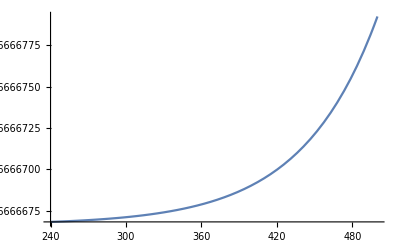

```mathematica
(*COVID-19 characteristics (world statistic-> we expect normal dis[t]tribution due to the central limitation theorem *)
(* https://www.worldometers.info/coronavirus/coronavirus-cases/#total-cases *)

tsic=30;(*coronavitus is present in Greece for 30 days as of today 28/3/202*)
(*for our first estimate we will consider that the attack rate for all 3 types of infectants is the same *)
(*We we will use the upper limit proposed by WHO, 2.5 R0  *)

atr[t_] :=(0.25)((1+(t/1460))/100);(*mortality : https://coronavirus.jhu.edu/map.html 28-03-2020)*)

(*At 28-03-2020 we had 966 confirmed cases, we suppose that there were at least 2000 sick people, either infected or asyptomatic*)

sig[t_]:=1/t0 *(1+t/120);(*carriers who fall sick*) (*one per day for a 14 day cycle*)

b1 =2.415;(* carrier spreading rate*)(*for the period that the daily cases where rising, the linear approximation had the inclination a=2.415*)
b2 =2.415/5;(* infected spreading rate*)(* infected spreading rate is the 1/5 of the carriers, due to people avoiding them ,on the basis of their symptoms*)


k2 =1-atr[t];(*cured infected *)
k1=1/3; (* based on SARS models*)


(**)
tquar=60;(*quarantine/isolation/social dis[t]tancing duration*)
rec=1/t0; (*each individual is considered susceptible after on life sycle od COVID*)
qu=9.5/10; (*quarantined patients*)
ttq[t_]:=(1/tquar) +((Exp[(t-210)/60]))/(10^9) ;
(* one person per tquar days returns to the susceptibles team*)
Plot[ttq[t],{t,240,500}]
```

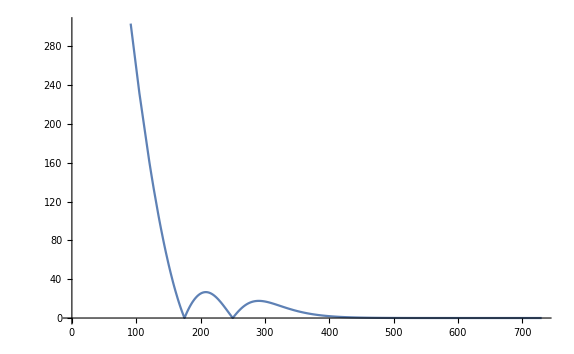

```mathematica
dis[t_]:=1000 (Abs[(175-t)/175]Abs[(1-(t/250))]*(1/(Exp[(t-250)/25]+1)));(*social dis[t]tancing -> 1000 people per percentage of sick people in the whole populace*)
Plot[dis[t],{t,1,730}]
```

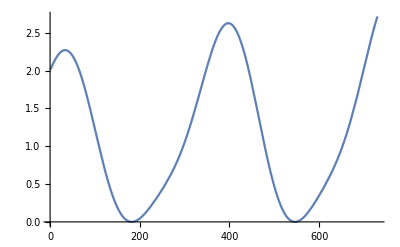

```mathematica
(* Our estimate of the safety parameter due to prevention from the use of masks,gloves etc *)

T=0.30;

(* Tourist influx parameter*)
tt[t_]:=Abs[Sin[Pi*(t/365)]]*(1/(Exp[(t-450)/15]+1));

(*Seasonality*)
mt[t_]:=Exp[t/2500]; (* Mutation*)
tp[t_]:=mt[t]*(1+(2/5)*Sin[Pi*(t/(182))])*(1+Cos[Pi*((t)/(182))]);  (* Διορθωση εξοδου στα χωρια*)

Plot[tp[t],{t,1,730}]
```

```mathematica
(* initial conditions*)
i0=10;
e0=0;
s0=0;
s0=N0-i0-e0;

(*one year*)
tmax=365;
```

```mathematica
sol=NDSolve[{s'[t]==P+1000*tt[t]-m*s[t]-T*(b1*tp[t]*e[t]+b2*tp[t]*i[t])*s[t]/(s[t]+i[t]+e[t] +r[t]+d[t])-dis[t]*s[t]*i[t]/(s[t]+i[t]+e[t] +r[t]+d[t])+rec*r[t] +ttq[t]*d[t],
e'[t]==50*tt[t]-(m+k1+sig[t])*e[t]+T*(b1*tp[t]*e[t]+b2*tp[t]*i[t])*s[t]/(s[t]+i[t]+e[t] +r[t]+d[t])-dis[t]*e[t]*i[t]/(s[t]+i[t]+e[t] +r[t]+d[t]),
i'[t]==sig[t]*e[t]-m*i[t]-atr[t]*i[t]-k2*i[t]-qu*i[t],
r'[t]==k1*e[t]+k2*i[t]-m*r[t]-rec*r[t],d'[t]==dis[t]*(e[t]+s[t])*i[t]/(s[t]+i[t]+e[t] +r[t]+d[t])+qu*i[t]-ttq[t]*d[t],
 s[1]==s0,e[1]==e0,i[1]==i0,r[1]==0,d[1]==0},{s[t],e[t],i[t],r[t],d[t]},{t,1,1000},MaxSteps->Infinity];
```

```mathematica
ssol[t_]:=s[t]/.sol[[1,1]];
esol[t_]:=e[t]/.sol[[1,2]];
isol[t_]:=i[t]/.sol[[1,3]];
rsol[t_]:=r[t]/.sol[[1,4]];
dsol[t_]:=d[t]/.sol[[1,5]];
```

```mathematica
(*spreading rate without prevention*)
R0=((b1+b2)/(2m+sig[t]+1+k1));
Print["R0 ="]
R0//N
(*spreading rate with prevention*)

RT=(T(b1+b2)/(2m+sig[t]+1+k1));
Print["RT ="]
RT//N

Print["Number of Deaths (Yearly):"]
Integrate[atr[t]*isol[t],{t,1,460}]//N
sol;
```

R0 =

2.898/(1.33339+0.142857 (1.+0.00833333 t))

RT =

0.8694/(1.33339+0.142857 (1.+0.00833333 t))

Number of Deaths (Yearly):

12569.

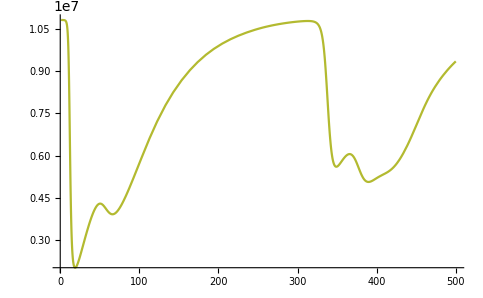

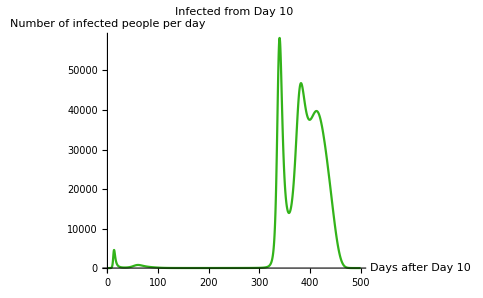

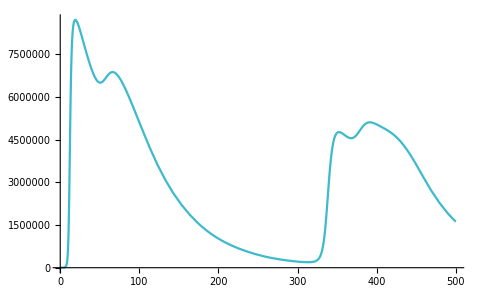

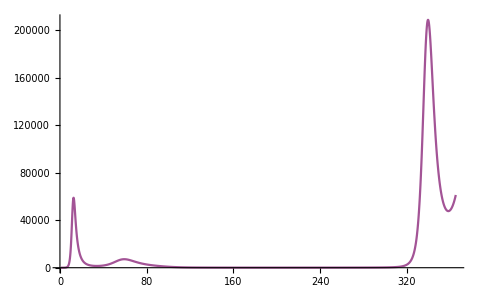

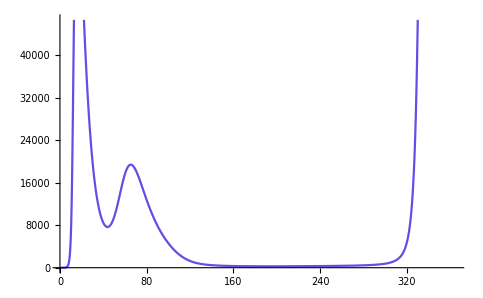

```mathematica
Plot[ssol[t],{t,1,500},PlotStyle->RGBColor[0.7,0.73,0.19]]
Plot[isol[t],{t,1,500},PlotStyle->RGBColor[0.2,0.7,0.1],PlotRange->All,PlotLabel->"Infected from Day 10",AxesLabel->{"Days after Day 10" , "Number of infected people per day"}]
Plot[dsol[t],{t,1,500},PlotStyle->RGBColor[0.24,0.73,0.8]]
Plot[esol[t],{t,1,tmax},PlotStyle->RGBColor[0.64,0.33,0.59],PlotRange->All]
Plot[rsol[t],{t,1,tmax},PlotStyle->RGBColor[0.4,0.3,0.9]]
```

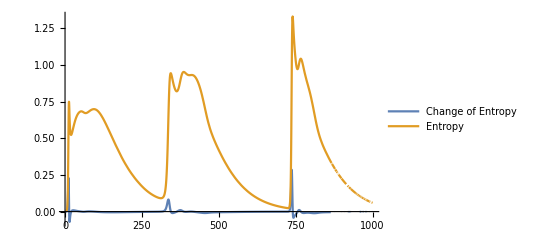

```mathematica
Nn[t_]=(ssol[t]+isol[t]+rsol[t]+esol[t]+dsol[t])^(-1);
sn[t_]=ssol[t]*Nn[t];
rn[t_]=rsol[t]*Nn[t];
in[t_]=isol[t]*Nn[t];
en[t_]=esol[t]*Nn[t];
dn[t_]=dsol[t]*Nn[t];

Sen[t_]:=-(sn[t]*Log[sn[t]]+en[t]*Log[en[t]]+rn[t]*Log[rn[t]]+in[t]*Log[in[t]]+dn[t]*Log[dn[t]])
DSen[t_]:=Sen[t]-Sen[t-1]
Plot[{DSen[t],Sen[t]},{t,2,1000},PlotLegends->{"Change of Entropy","Entropy"} ]
```

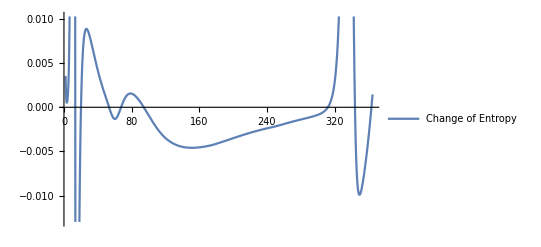

```mathematica
Plot[{DSen[t]},{t,2,tmax},PlotLegends->{"Change of Entropy"} ]
```

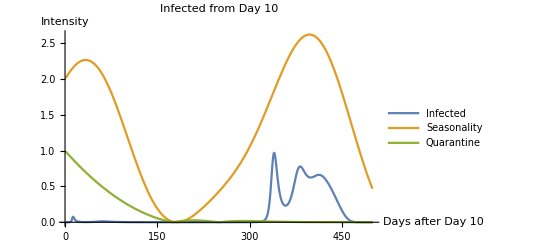

```mathematica
Plot[{isol[t]/(60000),tp[t],dis[t]/1000},{t,1,500},PlotRange->All,PlotLabel->"Infected from Day 10",AxesLabel->{"Days after Day 10" , "Intensity"},PlotLegends->{"Infected","Seasonality","Quarantine"}]
```